```mathematica
PrependTo[$Path, "~/myWork/npmma"];
Remove /@ Contexts["Cosmology*"];
```

```mathematica
<<Cosmology`
```

```mathematica
?zeqEH
```

zeqEH[cosmo] returns the equality redshift (Eq. 2, EH98)

```mathematica
zeqEH[FoMSWG]
```

3190.33

```mathematica
?keqEH
```

keqEH[cosmo] returns k_eq in Mpc^-1 (Eq. 3, EH98)

```mathematica
keqEH[FoMSWG]
```

0.00970417

```mathematica
?zdecEH
```

zdecEH[cosmo] returns the decoupling redshift (Eq. 4, EH98)

```mathematica
zdecEH[FoMSWG]
```

1020.49

```mathematica
rsEH[FoMSWG]
```

153.567

```mathematica
?rsEH
```

rsEH[cosmo] returns the sound horizon in Mpc(Eq.6, EH98)

```mathematica
rs0 = rsEH[FoMSWG]
```

153.567

```mathematica
?tkEH
```

tkEH[k, rs, cosmo] returns the transfer fn at k (in h^-1 Mpc)
    We explicitly pass in the sound horizon to save caching it --- this of course
    is trivial to simplify.

```mathematica
tkEH[0.1, rs0, FoMSWG]
```

0.111955

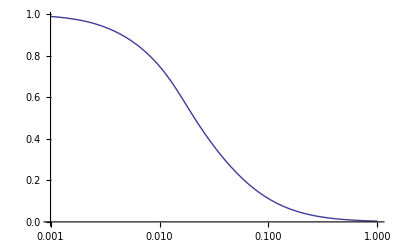
{0.074246,-Graphics-}

```mathematica
LogLinearPlot[(tkEH[#, rs0, FoMSWG]&)[k], {k, 0.001, 1.0}] //Timing
```